```mathematica
<<Notation`
Symbolize[Subscript[x_, y_]]
```

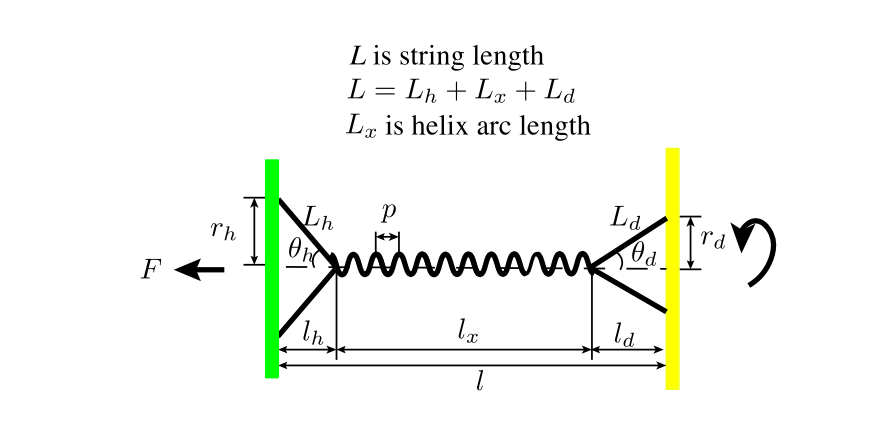

### Euler-Lagrange equation

U[ϕ(t)] = -2F(t) δ(ϕ(t))
T[ϕ(t)] = 1/2 J ϕ'(t)^2
where J =m_d/2 R_d^2
ℒ =T-U
= 1/2 m_d/2 R_d^2 ϕ'(t)^2+2F(t) δ(ϕ(t))

```mathematica
<<VariationalMethods`
ClearAll[δ]
```

```mathematica
EulerEquations[1/2 Subscript[m, d]/2 Subscript[R, d]^2 ϕ'[t]^2+2F[t] (δ[ϕ[t]]),ϕ[t],t]
```

2 F[t] δ'[ϕ[t]]-1/2 m_d R_d^2 ϕ''[t]==0

```mathematica
δ[ϕ1_]:=Piecewise[{{L-Sqrt[L^2-2 Subscript[r, d]^2+2 Subscript[r, d]^2 Cos[ϕ1]],-π<ϕ1<π}},L-√(L^2-(Subscript[r, d]+Subscript[r, h]+(Sqrt[ϕ1^2]-π)Subscript[ρ, s])^2)];(*Accurate expression*)
δ[ϕ1_]:=L-√(L^2-(Subscript[r, d]+Subscript[r, h]+(Sqrt[ϕ1^2])Subscript[ρ, s])^2);(*approximated expression*)
```

### Comparison with Experiments

#### Set the working directory as the directory where the notebook file is located. The data files are stored in directory “./Data_Eli _Jun22”.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/wenqiangfang/Dropbox (Brown)/research/BuzzButtonModel

#### Import and extract force F(t) data from files

```mathematica
rawdata=Import["Data_Eli_Jun22/inputForceData.csv"];
RawForceData=rawdata[[2;;,{1,2}]];
ForceData = RawForceData[[Complement[Range[Length@RawForceData],Flatten@Position[RawForceData[[;;,2]],""]]]];
```

#### Interpolate Force as a function of Time t

```mathematica
Force= Interpolation[ForceData]
```

InterpolatingFunction[…]

#### Plot Force data and F(t) interpolation

```mathematica
FitForce[t_]:=Piecewise[{{70 Sin[π/2(t-8)]^2,8<t<10},
{75 Sin[π/2(t-10.8)]^2,10.8<t<12.8},
{68 Sin[π/2(t-13.5)]^2,13.5<t<15.5},
{70 Sin[π/2(t-16)]^2,16<t<18},
{77 Sin[π/2(t-19)]^2,19<t<21},
{77 Sin[π/1.5(t-21.5)]^2,21.5<t<23},
{77 Sin[π/2(t-24)]^2,24<t<26},
{75 Sin[π/2(t-26.5)]^2,26.5<t<28.5}
},0]
```

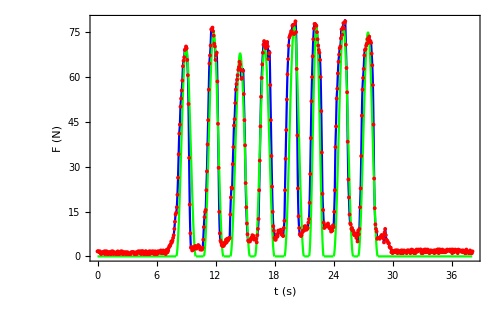

```mathematica
Show[Plot[{Force[t],FitForce[t]},{t,0,38.1}
,PlotStyle->{Blue,Green}
,PlotRange->All
,ImageSize->500
,GridLines->None,Axes->False
,Frame->True,FrameStyle->Directive[FontFamily->"Times",20],FrameLabel->{Style["t (s)",Black,FontFamily->"Times",24],Style["F (N)",Black,FontFamily->"Times",24]}
,RotateLabel->True]
,ListPlot[ForceData,PlotStyle->Red]
]
```

#### Prediction of the angular velocity

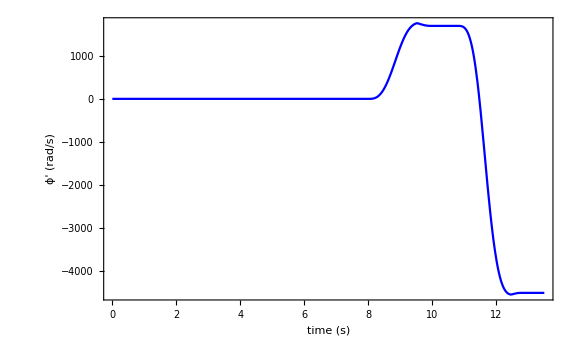

```mathematica
Block[{Subscript[ρ, s]=0.0005
,Subscript[r, h]=0.008
,Subscript[r, d]=0.004
,L=0.23
,Subscript[ϕ, 0]=-2π*20 (*Unknown*)
,Subscript[ω, 0]=0
,Subscript[m, d]=0.1004
,Subscript[R, d]=0.041
,Subscript[w, d]=QuantityMagnitude[Quantity[.3,"Inches"],"Meters"]
,F
,t1=38},
F[t_]:=-FitForce[t];
(*F[t_]:=-75 Piecewise[{{1,8<t<29.3}},0];*)
(*δ[ϕ1_]:=Piecewise[{{L-Sqrt[L^2-2 Subscript[r, d]^2+2 Subscript[r, d]^2 Cos[ϕ1]],-π<ϕ1<π}},L-√(L^2-(Subscript[r, d]+Subscript[r, h]+(Sqrt[ϕ1^2]-π)Subscript[ρ, s])^2)];*)
δ[ϕ1_]:=L-√(L^2-(Subscript[r, d]+Subscript[r, h]+(Sqrt[ϕ1^2])Subscript[ρ, s])^2);
Sol=NDSolve[{1/2 Subscript[m, d]  Subscript[R, d]^2  ϕ''[t]==2F[t]* (δ'[ϕ[t]]),ϕ[0]==Subscript[ϕ, 0],ϕ'[0]==Subscript[ω, 0]},ϕ,{t,0,t1}];
Plot[
{(*AngleVelocity[t](2π)/60.,*)60/(2π)Evaluate[ϕ'[t]/.Sol[[1]]]}
(*{2 π turnsf[t],ϕ[t]/.Sol[[1]]}*)
,{t,0,t1}
,PlotStyle->{Red,Blue}
,ImageSize->Large
,PlotRange->All
,GridLines->None,Axes->False,AxesStyle->Directive[Black,FontFamily->"Times",24]
,Frame->True,FrameStyle->Directive[FontFamily->"Times",20]
,FrameLabel->{Style["time (s)",Black,FontFamily->"Times",24],Style["ϕ' (rad/s)",Black,FontFamily->"Times",24]}
,RotateLabel->False]
]
```

#### Import and extract angular velocity ω(t) data from files

```mathematica
rawdata=Import["Data_Eli_Jun22/Button Speed Data.xlsx"];
 RawAVData=rawdata[[1,2;;,{3,2}]];(*The unit is rpm *)
Pos=Flatten@Position[RawAVData[[;;,2]],x_/;Abs[x]>0.0001];
AVData= RawAVData[[Pos]];
```

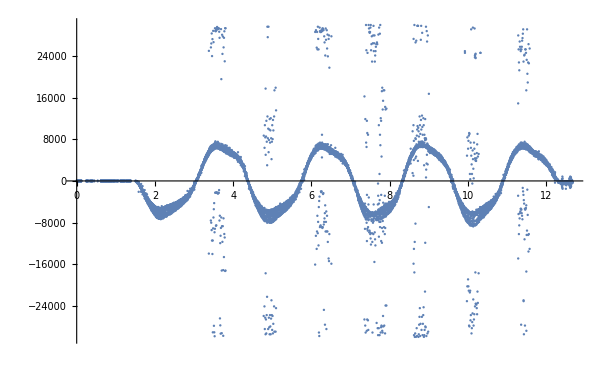

```mathematica
ListPlot[AVData]
```

#### Extract String Length Data

```mathematica
rawdata=Import["Data_Eli_Jun22/String Length Data.xlsx"];
Dispdata = rawdata[[1,5;;,{1,2}]];
Disp = Interpolation[Dispdata];(*The unit is cm/s *)
```

#### Plot the displacement data

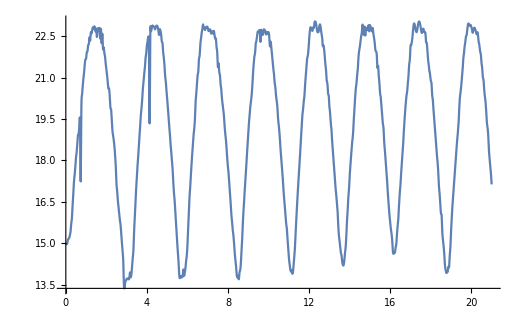

```mathematica
Plot[Disp[t],{t,0,21}]
```

#### Plot and check the displacement-rotation relation

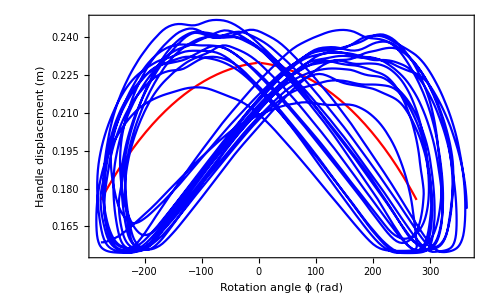

```mathematica
Block[{Subscript[ρ, s]=0.0005
,Subscript[r, h]=0.008
,Subscript[r, d]=0.004
,L=0.23
,x},
δ[ϕ1_]:=Piecewise[{{L-Sqrt[L^2-2 Subscript[r, d]^2+2 Subscript[r, d]^2 Cos[ϕ1]],-π<ϕ1<π}},L-√(L^2-(Subscript[r, d]+Subscript[r, h]+(Sqrt[ϕ1^2]-π)Subscript[ρ, s])^2)];
Show[
Plot[L-δ[ϕ],{ϕ,-44*2π,44*2π}
,PlotStyle->{Red}
,PlotRange->All
,ImageSize->1000
,GridLines->None,Axes->False
,Frame->True,FrameStyle->Directive[FontFamily->"Times",20],FrameLabel->{Style["Rotation angle ϕ (rad)",Black,FontFamily->"Times",24],Style["Handle displacement (m)",Black,FontFamily->"Times",24]}
,RotateLabel->True],
ParametricPlot[{ 2π Turns[t],Disp[t]/100},{t,0,70},PlotStyle->Blue,AspectRatio->1]
]
]
```

## Make videos of helix

### Helix equation (in local coordinate system)

x=ρ_x Cos[ϕ]
y=p/(2 π)ϕ
z=ρ_x Sin[ϕ]

### Geometric relations

L =L_h+L_x+L_d
L_h=r_h/Sin[θ_h]
L_d=r_d/Sin[θ_d]
L_x=Sqrt[(2π ρ_s)^2+p^2]ϕ/(2π)
l =l_h+l_x+l_d
l_h=r_h/Tan[θ_h]
l_d=r_d/Tan[θ_d]
l_x=ϕ/(2π) p
δ=L-l

### Constraints:

1. Two strings contact with each other: ρ_x=ρ_s
2. Strings cannot penetrate in pitch direction: p ≥ 4 ρ_s (there is a maximum number of rotations)
3. Force balance: θ_h = θ_d

#### Find out

U(ϕ,F;p,θ)=-F δ(ϕ;p,θ)
=-F(L-l(ϕ;p,θ))
=F l(ϕ;p,θ)-F L

min_(p,θ) U(ϕ,F;p,θ)
=min_(p,θ) [F l(ϕ;p,θ)-F L]
=F (min_(p,θ) l(ϕ;p,θ))-F L

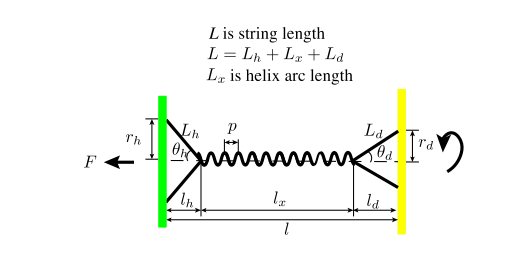

```mathematica
Block[(*{n = 150,Subscript[r, h]=0.00508,Subscript[r, d]=0.00508,Subscript[ρ, s]=0.000375,L=0.5},*)
{Subscript[ρ, s]=1,Subscript[r, h]=5,Subscript[r, d]=5,L=100,ϕ=2π},
ClearAll[θ,p];
NMinimize[{Subscript[r, h]/Tan[θ]+Subscript[r, d]/Tan[θ]+ϕ/(2π) p,Subscript[r, h]/Sin[θ]+Subscript[r, d]/Sin[θ]+Sqrt[(2π Subscript[ρ, s])^2+p^2] ϕ/(2π)==L,L>p>4 Subscript[ρ, s],0<θ<π/2},{θ,p}]
]
```

### Subroutines

```mathematica
ClearAll[a,ϕ]
```

```mathematica
SimplifyRule= {Subscript[r, d]->a-ϕ Subscript[ρ, s]-Subscript[r, h]};
SimplifyRuleRev= {a->Subscript[r, d]+Subscript[r, h]+ϕ  Subscript[ρ, s]};
```

```mathematica
Solθ=(Solve[(Subscript[r, h]/Sin[θ]+Subscript[r, d]/Sin[θ]+Sqrt[(2π Subscript[ρ, s])^2+p^2] ϕ/(2π)==L),θ][[2]]/.C[1]->0)/.SimplifyRule
f[p_]:=Evaluate[(Subscript[r, h]/Tan[θ]+Subscript[r, d]/Tan[θ]+ϕ/(2π) p/.Solθ)]/.SimplifyRule//Simplify;
Solp1=Solve[(D[f[p],p]==0),p]//Simplify;
Solp2=Simplify[Solp1/.SimplifyRule,L>a>0][[2]]
lexpress=Simplify[f[p]/.Solp2/.SimplifyRule,{L>a>0,Subscript[ρ, s]>0,a>Subscript[ρ, s] ϕ}]
```

{θ→ArcSin[(2 π (-a+ρ_s ϕ))/(-2 L π+√(p^2+4 π^2 ρ_s^2) ϕ)]}

{p→(2 π √(-(a^2-L^2) ρ_s^2))/a}

√(-a^2+L^2)

```mathematica
Block[{Subscript[ρ, s]=1,Subscript[r, h]=5,Subscript[r, d]=5,L=100,n=4,ϕ,a},
ClearAll[p,θ];
ϕ=2π n;
a = Subscript[r, d]+Subscript[r, h]+Subscript[ρ, s] ϕ;
N@{Solθ/.Solp2,Solp2,lexpress}//TableForm
]
```

θ→0.358989
p→16.7441
93.6253

```mathematica
Sola=Solve[Evaluate[p/.Solp2]==4 Subscript[ρ, s],a]
```

{{a→-(L π)/(√(4+π^2))},{a→(L π)/(√(4+π^2))}}

```mathematica
Solϕ=Solve[Evaluate[a/.Sola[[2]]]==Subscript[r, d]+Subscript[r, h]+ϕ  Subscript[ρ, s],ϕ]//Simplify
```

{{ϕ→-(-(L π)/(√(4+π^2))+r_d+r_h)/ρ_s}}

```mathematica
Simplify[ArcSin[(2 π (-a+Subscript[ρ, s] ϕ))/(-2 L π+√(p^2+4 π^2 Subscript[ρ, s]^2) ϕ)]//.{p->(2 π √(-(a^2-L^2) Subscript[ρ, s]^2))/a,a->Subscript[r, d]+Subscript[r, h]+ϕ  Subscript[ρ, s]},Subscript[ρ, s]>0]
```

ArcSin[(r_d+r_h)/(L-ρ_s ϕ √(L^2/(r_d+r_h+ρ_s ϕ)^2))]

```mathematica
ArcCos[2/π]//N
```

0.880689

```mathematica
Cos[ArcSin[π/(√(4+π^2))]]//Simplify
```

2/(√(4+π^2))

```mathematica
RotationMatrix[ϕ,{0,1,0}].{((Subscript[l, x]+Subscript[l, d])-x)/Subscript[l, d] Subscript[ρ, s],x,(x-Subscript[l, x])Tan[θ]}
```

```mathematica
ClearAll[ϕshift,WhiteRed,ReflectionY,InextensibleModel]
ϕshift[x_]=Piecewise[{{x-π,x>π},{0,-π≤x≤π},{x+π,x<-π}}];
WhiteRed[z_]:=Piecewise[{{White,z>0},{Red,z≤0}}]
ReflectionY=ReflectionMatrix[{1,0,0}].ReflectionMatrix[{0,0,1}];
ReflectionX=ReflectionMatrix[{1,0,0}];
InextensibleModel[ϕ1_]:=Block[{Subscript[ρ, s]=1,Subscript[r, h]=5,Subscript[r, d]=5,L=100,ϕ=ϕshift@ϕ1,(*,Subscript[ϕ, x]=ϕshift[ϕ1]*)
,Subscript[l, x],Subscript[l, h],Subscript[l, d],a,p,θ,xzRange,yRange,disk,S1,S2
,ϕx,Helix,HelixSlope,HandleHole,DiskHole,HandleLinePts,HandleLine,DiskLinePts,DiskLine,HandleDisk,WholeString
,StringPlt,DiskLateral,DiskBase,HandleLateral,HandleBase
},
xzRange=2{-Max[Subscript[r, d],Subscript[r, h]],Max[Subscript[r, d],Subscript[r, h]]};
yRange={-L-10 Subscript[ρ, s],10 Subscript[ρ, s]};
ϕx[x_]:=2 π x/p;
Helix[x_]:={Subscript[ρ, s] Cos[ϕx[x]],x,Subscript[ρ, s] Sin[ϕx[x]]};
HelixSlope[x_]:= {-(2 π Subscript[ρ, s] Sin[ϕx[x]])/p,1,(2 π Subscript[ρ, s] Cos[ϕx[x]])/p};
HandleHole={0,-Subscript[l, h],-Subscript[r, h]};
DiskHole[ϕi_]:=RotationMatrix[ϕi,{0,-1,0}].{0,Subscript[l, d]+Subscript[l, x],-Subscript[r, d]};
HandleLinePts = {HandleHole,Helix[0]-Subscript[l, h]/4 HelixSlope[0],Helix[0]};
DiskLinePts = {Helix[Subscript[l, x]],Helix[Subscript[l, x]]+Subscript[l, d]/4 HelixSlope[Subscript[l, x]],DiskHole[ϕ1]};
WholeString[x_] :=If[ϕ==0,
Subscript[l, x]=0;
Subscript[l, h]=Sqrt[L^2-Norm[DiskHole[ϕ1]-DiskHole[0]]^2];
Subscript[l, d]=0;
HandleDisk = BSplineFunction[{HandleHole,DiskHole[ϕ1]}];
HandleDisk[x/Subscript[l, h]+1],
a=Subscript[r, d]+Subscript[r, h]+Subscript[ρ, s] Abs@ϕ;
p=Sign[ϕ]*N@((2 π Subscript[ρ, s] √(-(a^2-L^2)))/a);
θ=N@ArcSin[(2 π (-Subscript[r, d]-Subscript[r, h]))/(-2 L π+√(p^2+4 π^2 Subscript[ρ, s]^2) Abs[ϕ])];
Subscript[l, x]=ϕ/(2π) p;
Subscript[l, h]=Subscript[r, h]/Tan[θ];
Subscript[l, d]=Subscript[r, d]/Tan[θ];
HandleLine = BSplineFunction[HandleLinePts];
DiskLine = BSplineFunction[DiskLinePts];
Piecewise[{{HandleLine[x/Subscript[l, h]+1],x≤0},{Helix[x],0<x≤Subscript[l, x]},{DiskLine[(x-Subscript[l, x])/Subscript[l, d]],x>Subscript[l, x]}}]-{0,Subscript[l, d]+Subscript[l, x],0}
];
StringPlt=ParametricPlot3D[{WholeString[x],ReflectionY.WholeString[x]}
,{x,-Subscript[l, h],Subscript[l, d]+Subscript[l, x]}
,PlotStyle->{Directive[{Gray,Specularity[1,10]}],Directive[{Red,Specularity[1,10]}]}
,Lighting->"Neutral"
,PlotPoints->200
,MaxRecursion->3
,BoxRatios->Automatic
,PlotRange->{xzRange,yRange,xzRange}
,Axes->None,Boxed->False
(*,Method->{"TubePoints"->30}*)
,ViewPoint->Right]/.Line[pts_,rest___]:>Tube[pts,Subscript[ρ, s],rest];
DiskLateral =ParametricPlot3D[{1.5 Subscript[r, d] Cos[θ],y,1.5 Subscript[r, d] Sin[θ]},{θ,0,2π},{y,0,3 Subscript[ρ, s]}
,PlotStyle->{Specularity[1,10]}
,Mesh->None
,PlotPoints->100
,MaxRecursion->3
,ColorFunction->(WhiteRed[-#3Cos[-ϕ1]-#1 Sin[-ϕ1]]&)
,ColorFunctionScaling->False];
DiskBase=ParametricPlot3D[{r Cos[θ],0,r Sin[θ]},{r,0,1.5 Subscript[r, d] },{θ,0,2π}
,PlotStyle->{Specularity[1,10]}
,ColorFunction->(WhiteRed[-#3Cos[-ϕ1]-#1 Sin[-ϕ1]]&)
,Mesh->None
,PlotPoints->100
,MaxRecursion->3
,ColorFunctionScaling->False];
HandleLateral =ParametricPlot3D[{1.8 Subscript[r, d] Cos[θ],y-Subscript[l, h]-Subscript[l, d]-Subscript[l, x],1.8 Subscript[r, d] Sin[θ]},{θ,0,2π},{y,-3 Subscript[ρ, s],0}
,PlotStyle->{Specularity[1,10]}
,Mesh->None
,PlotPoints->100
,MaxRecursion->3
,ColorFunction->(WhiteRed[-#3]&)
,ColorFunctionScaling->False];
HandleBase=ParametricPlot3D[{r Cos[θ],(-Subscript[l, h]-Subscript[l, d]-Subscript[l, x]),r Sin[θ]},{r,0,1.8 Subscript[r, d] },{θ,0,2π}
,PlotStyle->{Specularity[1,10]}
,ColorFunction->(WhiteRed[-#3]&)
,Mesh->None
,PlotPoints->100
,MaxRecursion->3
,ColorFunctionScaling->False];
Show[StringPlt,DiskLateral,DiskBase,HandleLateral,HandleBase,ImageSize->{Automatic,200}]
]
```

```mathematica
ClearAll[InextensibleModel]
HelixList=Table[InextensibleModel[n],{n,1,11}]
SetDirectory[NotebookDirectory[]]
"/Users/wenqiangfang/Dropbox (Brown)/research/BuzzButtonModel"
Export["Helix_figures/helix"<>IntegerString[#]<>".pdf",HelixList[[#]]]&/@Range[11]
```

```mathematica
InextensibleModel[5]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
Figlist=Flatten[Import["Helix_figures/helix"<>IntegerString[#]<>".pdf"]&/@Range[11]];
```

```mathematica
Init=Import["Helix_figures/helix0.pdf"][[1]];
```

```mathematica
PrependTo[Figlist,Init];
```

### Video

```mathematica
Animate[Figlist[[n]],{n,Range[12]}]
```

```mathematica
δ'[ϕ]
```

Piecewise[{{-(ρ_s (r_d+r_h+ρ_s (-π-ϕ)))/(√(L^2-(r_d+r_h+ρ_s (-π-ϕ))^2)), ϕ<-π}, {(r_d^2 Sin[ϕ])/(√(L^2-2 r_d^2+2 r_d^2 Cos[ϕ])), -π<ϕ<π}, {(ρ_s (r_d+r_h+ρ_s (-π+ϕ)))/(√(L^2-(r_d+r_h+ρ_s (-π+ϕ))^2)), ϕ>π}, {Indeterminate, True}}]

```mathematica
δ[0]=L-√(L^2-(Subscript[r, d]+Subscript[r, h]-π Subscript[ρ, s])^2)
```

L-√(L^2-(r_d+r_h-π ρ_s)^2)

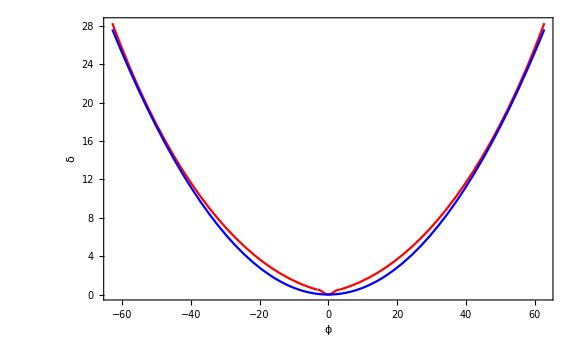

```mathematica
ClearAll[δ,ϕ,a,Subscript[ρ, s],Subscript[r, h],Subscript[r, d],L]
δ[ϕ1_]:=Piecewise[{{L-Sqrt[L^2-2 Subscript[r, d]^2+2 Subscript[r, d]^2 Cos[ϕ1]],-π<ϕ1<π}},L-√(L^2-(Subscript[r, d]+Subscript[r, h]+(Sqrt[ϕ1^2]-π)Subscript[ρ, s])^2)]
(*δ[ϕ1_]:=L-√(L^2-(Subscript[r, d]+Subscript[r, h]+(Sqrt[ϕ1^2]-π)Subscript[ρ, s])^2)*)
Block[{Subscript[ρ, s]=1,Subscript[r, h]=5,Subscript[r, d]=5,L=100},
Plot[{δ[ϕ](*,δ'[ϕ],δ''[ϕ]*),0.007(ϕ)^2},{ϕ,-20π,20π}
,PlotStyle->{Red,Blue,Green}
,PlotRange->Automatic
,ImageSize->Large
,GridLines->None,Axes->False,AxesStyle->Directive[Black,FontFamily->"Times",24],Frame->True,FrameStyle->Directive[FontFamily->"Times",20],FrameLabel->{Style["ϕ",Black,Italic,FontFamily->"Times",24],Style["δ",Black,Italic,FontFamily->"Times",24]},RotateLabel->False]
]
```

### e.g. Plot helix

```mathematica
(*p≥2/π*)
Block[{ρ=1,p=4/π,n=10,ζ,H1,H2},
ζ=p π;
H1 =ParametricPlot3D[{ρ Cos[ϕ],p ϕ,ρ Sin[ϕ]},{ϕ,0,2n π}
,PlotStyle->{Gray,Specularity[Gray,10]}
,Lighting->"Neutral"
,PlotPoints->100
,MaxRecursion->3
,PlotRange->{{-2ρ,2ρ},{-1,2n π p*1.1},{-2ρ,2ρ}}
,Axes->None,Boxed->False
,Method->{"TubePoints"->30}
,ViewPoint->Right]/.Line[pts_,rest___]:>Tube[pts,ρ,rest];
H2=ParametricPlot3D[{ρ Cos[ϕ],p ϕ+ζ,ρ Sin[ϕ]},{ϕ,-π,2n π-π}
,PlotStyle->{Red,Specularity[1,10]}
(*,Lighting->"Neutral"*)]/.Line[pts_,rest___]:>Tube[pts,ρ,rest];
Show[H1,H2,ImageSize->{Automatic,50}]
]
```